## Using PRIMAT. Posterior distribution for baryons abundance.

### Loading PRIMAT

Setting the notebook directory (in batch mode this is not evaluated because it seems to be the default one)

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we go the parent directory, or base directory of PRIMAT.

```mathematica
SetDirectory[ParentDirectory[Directory[]]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

We load PRIMAT. It takes some time because it starts reading the file with nuclear reactions and deduces which are the nuclides needed, 
and it starts to build formally the network of equations

```mathematica
Timing[<<PRIMAT-Main.m]
```

{16.8608,Null}

### Posterior in baryons

#### Launch of Monte-Carlo

```mathematica
$ParallelBool=True;

$RandomNuclearRates=True;
$Randomτneutron=True;
$Randomh2Ωb=False;

Meanh2Ωb0=h2Ωb0;
Tableω=Table[ω,{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0,1/2*σh2Ωb0}];
```

```mathematica
ComputePrincipalAbundanceBaryonsZoom[ω_]:=Module[{ResultMean,Resultσ,Meanh2Ωb0Old},
Meanh2Ωb0Old=Meanh2Ωb0;
Meanh2Ωb0=ω;

RunPRIMATMonteCarlo[LengthMC];

YP=4ElementColumn["a"];
YDH=10^5 ElementColumn["d"]/ElementColumn["p"];
YHe3H=10^5(ElementColumn["t"]+ElementColumn["He3"])/ElementColumn["p"];
YLi7H=10^10(ElementColumn["Li7"]+ElementColumn["Be7"])/ElementColumn["p"];

Meanh2Ωb0=Meanh2Ωb0Old;
{YP,YDH,YHe3H,YLi7H}

]
```

```mathematica
LengthMC=1000;
MachineNumerics=""(*$MachineName*);
```

We run the Monte - Carlo on the grid. Very long (hours, days)

```mathematica
Timing[TableYsLowMiddleUp3=ComputePrincipalAbundanceBaryonsZoom/@Tableω;];
Export["MonteCarlo/YsOmega"<>MachineNumerics<>".mx",TableYsLowMiddleUp3,"MX"];
```

Running a Monte-Carlo with 1000 points.

$Aborted

#### Results

Once this is over we load the results. We give the name of the machine on which this was performed

```mathematica
MachineOfRuns="";
```

```mathematica
TableYsLowMiddleUp3=Import["MonteCarlo/YsOmega"<>MachineOfRuns<>".mx"];
```

Import::nffil: File not found during Import.

```mathematica
TableYsLowMiddleUp3//Dimensions
```

{}

We interpolate the lowermiddle and upper quantiles, and also the mean and standard deviation

```mathematica
MyPair[a_,b_]:={a,b};
ValueLowω[i_]:=Thread[MyPair[Tableω,Flatten[Quantile[#,{0.15865}]&/@TableYsLowMiddleUp3[[All,i]]]]]
ValueMiddleω[i_]:=Thread[MyPair[Tableω,Flatten[Quantile[#,{0.50}]&/@TableYsLowMiddleUp3[[All,i]]]]]
ValueHighω[i_]:=Thread[MyPair[Tableω,Flatten[Quantile[#,{1-0.15865}]&/@TableYsLowMiddleUp3[[All,i]]]]]
ValueMeanω[i_]:=Thread[MyPair[Tableω,Flatten[Mean[#]&/@TableYsLowMiddleUp3[[All,i]]]]]
Valueσω[i_]:=Thread[MyPair[Tableω,Flatten[StandardDeviation[#]&/@TableYsLowMiddleUp3[[All,i]]]]]
```

The likelihood for observed abundances

```mathematica
LikeliHood[{Yobs_,σobs_}][Yth_]:=1/(√(2π)σobs)Exp[(-(Yth-Yobs)^2)/(2 σobs^2)]
```

The prior from CMB on abundances

```mathematica
PostCMB[h2Ωb0_]:=With[{δh2Ωb0=h2Ωb0-Meanh2Ωb0},1/(√(2π)σh2Ωb0)Exp[(-(δh2Ωb0)^2)/(2 σh2Ωb0^2)]];
```

This is to mimic codes which obtain 2.61 instead of 2.46 in D/H.

```mathematica
FakeWrongDeuterium:=0(*-0.15*);
```

The posterior from BBN

```mathematica
σObsYHeCorrect=0.0040;
YHeobsCorrect=0.2449;

σObsYHeBAD=0.0022;
YHeobsBAD=0.2551;
```

```mathematica
YHeobs=YHeobsCorrect;
σObsYHe=σObsYHeCorrect;
```

```mathematica
σObsDH=0.030;
YDHObs=2.527;
```

```mathematica
Meanh2Ωb0=Meanh2Ωb0Planck
```

0.02225

```mathematica
Clear[LogPostBBNω]
LogPostBBNω[{YP_,σYP_}]:=LogPostBBNω[{YP,σYP}]=Interpolation[Transpose[{Tableω,Log[(Mean[LikeliHood[{YP,σYP}][#[[1]]]*
LikeliHood[{YDHObs+FakeWrongDeuterium,σObsDH}][#[[2]]]])&/@TableYsLowMiddleUp3]}],InterpolationOrder->3];
```

```mathematica
PosteriorRawω[ω_]:=Exp@LogPostBBNω[{YHeobs,σObsYHe}][ω]PostCMB[ω]
PosteriorRawBADω[ω_]:=Exp@LogPostBBNω[{YHeobsBAD,σObsYHeBAD}][ω]PostCMB[ω]

PosteriorRawBBNω[ω_]:=Exp@LogPostBBNω[{YHeobs,σObsYHe}][ω]
PosteriorRawBBNBADω[ω_]:=Exp@LogPostBBNω[{YHeobsBAD,σObsYHeBAD}][ω]
```

```mathematica
Clear[NormPosteriorω,NormPosteriorBADω]
NormPosteriorω=NIntegrate[PosteriorRawω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}];
NormPosteriorBADω=NIntegrate[PosteriorRawBADω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}];
```

NIntegrate::inumr: The integrand 2493.39 ⅇ^(-1.95312×10^7 (-0.02225+ω)^2«1»Interpolation[Transpose[{{0.02097,0.02105,0.02113,0.02121,0.02129,0.02137,0.02145,0.02153,«14»,0.02273,0.02281,0.02289,0.02297,0.02305,0.02313,0.02321},Log[«7»]}],«1»]«1»«1»]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.02097,0.02321}}.

```mathematica
Clear[NormPosteriorBBNω,NormPosteriorBBNBADω]
NormPosteriorBBNω=NIntegrate[PosteriorRawBBNω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}];
NormPosteriorBBNBADω=NIntegrate[PosteriorRawBBNBADω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}];
```

```mathematica
Posteriorω[ω_]:=PosteriorRawω[ω]/NormPosteriorω
PosteriorBADω[ω_]:=PosteriorRawBADω[ω]/NormPosteriorBADω

PosteriorBBNω[ω_]:=PosteriorRawBBNω[ω]/NormPosteriorBBNω
PosteriorBBNBADω[ω_]:=PosteriorRawBBNBADω[ω]/NormPosteriorBBNBADω
```

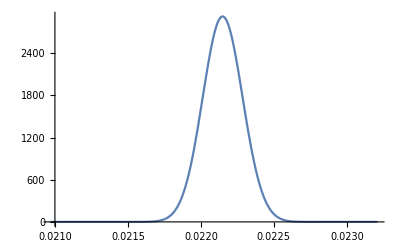

```mathematica
Plot[Posteriorω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]
```

Means and standard deviations

```mathematica
MeanPosteriorBBNω=NIntegrate[ω PosteriorBBNω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]
SigmaPosteriorBBNω=Sqrt[NIntegrate[(ω-MeanPosteriorBBNω)^2 PosteriorBBNω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]]
```

0.0219034

0.000250209

```mathematica
MeanPosteriorω=NIntegrate[ω Posteriorω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]
SigmaPosteriorω=Sqrt[NIntegrate[(ω-MeanPosteriorω)^2 Posteriorω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]]
```

0.0221502

0.000136455

```mathematica
MeanPosteriorBADω=NIntegrate[ω PosteriorBADω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]
SigmaPosteriorBADω=Sqrt[NIntegrate[(ω-MeanPosteriorBADω)^2 PosteriorBADω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]]
```

0.022165

0.000137127

```mathematica
NIntegrate[ω PosteriorBBNω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}]
```

0.0219034

```mathematica
Maxω=FindMaximum[Posteriorω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}][[2,1,2]]
MaxBBNω=FindMaximum[PosteriorBBNω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}][[2,1,2]]
MaxBADω=FindMaximum[PosteriorBADω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}][[2,1,2]]
MaxBBNBADω=FindMaximum[PosteriorBBNBADω[ω],{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0}][[2,1,2]]
```

0.0221488

0.0218956

0.0221632

0.0219404

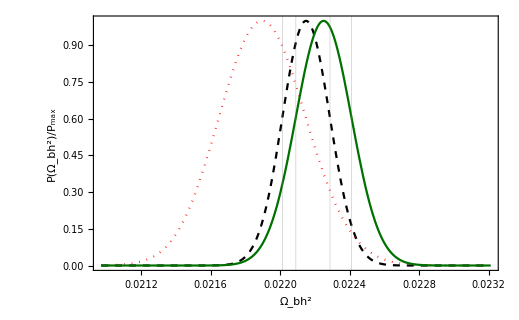

```mathematica
PosteriorPlotω=Plot[{Posteriorω[ω]/Posteriorω[Maxω],PosteriorBBNω[ω]/PosteriorBBNω[MaxBBNω],PostCMB[ω]/PostCMB[Meanh2Ωb0](*,PosteriorBADω[ω]/PosteriorBADω[MaxBADω],PosteriorBBNBADω[ω]/PosteriorBBNBADω[MaxBBNBADω]*)},{ω,Meanh2Ωb0-8σh2Ωb0,Meanh2Ωb0+6σh2Ωb0},Frame->True,GridLines->{{{Meanh2Ωb0-σh2Ωb0,{Darker@Gray,Thick}},{Meanh2Ωb0+σh2Ωb0,{Darker@Gray,Thick}},{MeanPosteriorω-SigmaPosteriorω,{Darker@Gray,Thick,Dashed}},
{MeanPosteriorω+SigmaPosteriorω,{Darker@Gray,Thick,Dashed}}},{}},PlotStyle->{{Black,Dashed},{Red,Dotted},{Darker@Darker@Green},{Blue},{Blue,Dashed}},FrameLabel->{"Ω_bh^2","P(Ω_bh^2)/P_max"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004]]
Export["Plots/PosteriorPlotw.pdf",Style[PosteriorPlotω,Magnification->1],"PDF"];
```